```mathematica
Integrate[(t-4/3 t^2)*(t^3+2/5 t-4/3 t^2),{t,0,1}]
```

0

```mathematica
Integrate[(t-4/3 t^2)*t^3,{t,0,1}]/Integrate[(t-4/3 t^2)*(t-4/3 t^2),{t,0,1}]
```

-1

```mathematica
list2
```

{1294,1279,1274,1264,1263,1254,1251,1251,1248,1240,1232,1220,1218,1210}

```mathematica
list3
```

{1284,1272,1256,1254,1242,1274,1264,1256,1250}

```mathematica
{Length[list2],Length[list3]}
```

{14,9}

```mathematica
(Mean[list2]-Mean[list3])/(√(Variance[list2]/14+Variance[list3]/9))//N
```

-1.45988

```mathematica
(Variance[list2]/14+Variance[list3]/9)^2/(Variance[list2]^2/(14^2*13)+Variance[list3]^2/(81*8))//N
```

20.636

```mathematica
Variance[list2]/Variance[list3]//N
```

3.36001

```mathematica
Sqrt[9*1.85*0.00001-5*1.5*0.001/(2*981*9.8*19.33)]
```

```mathematica
Solve[{-A w^2+2 β B w+w0^2 A==M/J,-B w^2-2 β A w+w0^2 B==0},{A,B}]
```

{{A→-(M (w^2-w0^2))/(J (w^4-2 w^2 w0^2+w0^4+4 w^2 β^2)),B→(2 M w β)/(J (w^4-2 w^2 w0^2+w0^4+4 w^2 β^2))}}

```mathematica
ff
```

```mathematica
list=Log[#]&/@list
```

{Log[141],Log[140],Log[139],Log[137],Log[136],Log[135],Log[134],Log[133],Log[131],Log[130],Log[129],Log[128],Log[127],Log[125],Log[124],Log[123],Log[122],Log[121],Log[120],Log[119],Log[117],Log[117],Log[115],Log[114],Log[113],Log[112],Log[111],Log[110],Log[109],Log[108],Log[107],Log[105],Log[105],Log[103],Log[103],Log[102],Log[101],Log[99],Log[99],Log[97],Log[97],Log[95],Log[94],Log[93],Log[93],Log[91],Log[91],Log[89],Log[89],Log[88]}

```mathematica
list={141,140,139,137,136,135,134,133,131,130,129,128,127,125,124,123,122,121,120,119,117,117,115,114,113,112,111,110,109,108,107,105,105,103,103,102,101,99,99,97,97,95,94,93,93,91,91,89,89,88,87};
```

```mathematica
Length[list]
```

51

```mathematica
(Sum[list[[i]],{i,26,50}]-Sum[list[[i]],{i,1,25}])/625//N
```

-0.00966266

```mathematica
x/.NSolve[%249==-2 π/(√(1/x^2-1)),x][[2]]
```

0.0131386

```mathematica
NSolve[%249==-2 π/(√(1/x^2-1)),x]
```

{{x→0.00153786},{x→-0.00153786}}

```mathematica
list2={14.436,14.44,14.443,14.445,14.447};Mean[list2]/10
```

1.44422

```mathematica
(2π)/(1.444*√(1-%249^2))
```

4.35124

```mathematica
0.013138581883803053
```

```mathematica
w0=4.35124;ζ=0.013245518194393529;
```

```mathematica
ζ=-ζ
```

0.0162584

```mathematica
αm=142*2*ζ*√(1-ζ^2)
```

4.61678

```mathematica
144*√(1-2*ζ^2)
```

143.006

```mathematica
4*ζ^2
```

2.10815

```mathematica
αm=142*2*ζ*√(1-ζ^2)
f[w_]:=αm/(√(4*ζ^2*(1.444/w)^2+(1-(1.444/w)^2)^2));
```

-0.054075

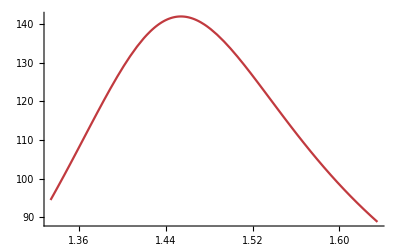

```mathematica
1-2*ζ^2
```

```mathematica
f[1.441]
```

177.436

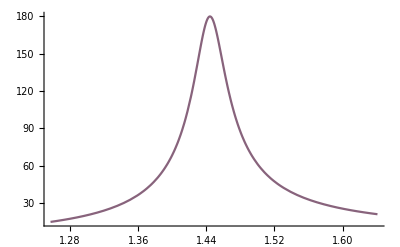

```mathematica
Plot[f[x],{x,1.257,1.641},PlotRange->All,ColorFunction->"Rainbow"]
```

```mathematica
list3=Log[#]&/@{133,122,113,104,96,88,81,75,69,63};(Sum[list3[[i]],{i,6,10}]-Sum[list3[[i]],{i,1,5}])/5//N
```

```mathematica
0.2*Sqrt[(Sum[(list3[[i+5]]-list3[[i]]-%467)^2,{i,1,5}])/4]//N
```

0.000979755

```mathematica
D[√(1/(1+(4π^2)/x^2)),x]//Simplify
```

(4 π^2 (1/(1+(4 π^2)/x^2))^(3/2))/x^3

```mathematica
%470
```

```mathematica
(*ζ*)
```

0.0131386

```mathematica
%470/%196
```

0.0030195

```mathematica
%473/(2*%474^2)
```

0.451656

```mathematica
1/(2*%474)
```

38.0559

```mathematica
(%469/.x->%470)*%468
```

```mathematica
(*Δζ*)
```

0.000155932

```mathematica
%473/%196
```

0.0000358362

0.000979755 ((4 π^2 (1/(1+(4 π^2)/x^2))^(3/2))/x^3/.0.0131386)

```mathematica
list3//N
```

{4.89035,4.80402,4.72739,4.64439,4.56435,4.47734,4.39445,4.31749,4.23411,4.14313,4.06044,3.97029,3.89182,3.80666}

```mathematica
-325/49//N
```

-6.63265

```mathematica
list=Drop[list,-1]
```

{141,140,139,137,136,135,134,133,131,130,129,128,127,125,124,123,122,121,120,119,117,117,115,114,113,112,111,110,109,108,107,105,105,103,103,102,101,99,99,97,97,95,94,93,93,91,91,89,89,88}

```mathematica
list4=1.444/{1.441,1.439,1.438,1.435,1.432,1.429,1.425,1.421,1.410,1.401,1.389,1.378,1.359,1.293,1.257,1.448,1.450,1.456,1.461,1.465,1.472,1.48,1.49,1.50,1.512,1.535,1.567,1.632,1.641};
list5={90,95.75,104.25,113.5,119.5,127.25,135.75,140,150.75,155.25,160.5,163,165.75,169.5,170.75,70.5,64.5,54.5,46,40.5,33,27,21,16.5,13.5,10,7,4,3.25};
```

```mathematica
list4
```

{1.00208,1.00347,1.00417,1.00627,1.00838,1.0105,1.01333,1.01619,1.02411,1.03069,1.0396,1.0479,1.06255,1.11678,1.14877,0.997238,0.995862,0.991758,0.988364,0.985666,0.980978,0.975676,0.969128,0.962667,0.955026,0.940717,0.921506,0.884804,0.879951}

```mathematica
Length/@{list4,list5}
```

{29,29}

```mathematica
{list4,list5}//Transpose
```

{{1.441,180},{1.439,179},{1.438,174},{1.435,165},{1.432,154},{1.429,139},{1.425,121},{1.421,109},{1.41,82},{1.401,67},{1.389,55},{1.378,45},{1.359,35},{1.293,18},{1.257,14},{1.448,173},{1.45,166},{1.456,150},{1.461,133},{1.465,122},{1.472,103},{1.48,86},{1.49,72},{1.5,60},{1.512,50},{1.535,39},{1.567,30},{1.632,22},{1.641,21}}

```mathematica
ListInterpolation[list5,{list4}]
```

InterpolatingFunction[{{0.879951, 1.14877}}, <>]

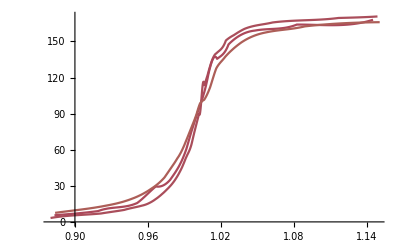

```mathematica
Show[%548,%573,%588]
```

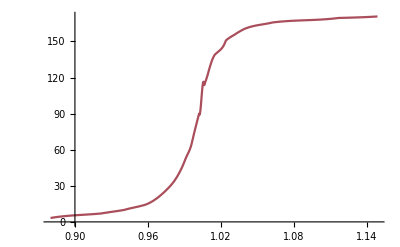

```mathematica
Plot[%538[x],{x,0.8799512492382693,1.1487669053301512},ColorFunction->"Rainbow"]
```

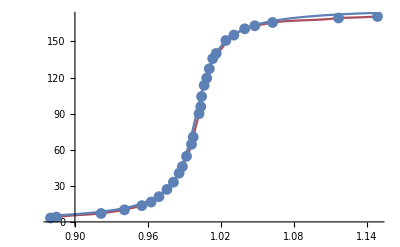

```mathematica
Show[%548,%554,ListPlot[{list4,list5}//Transpose]]
```

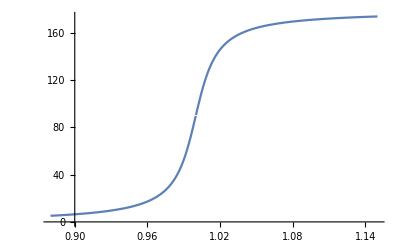

```mathematica
Plot[Piecewise[{{180/π*ArcTan[(2*0.0132)/((1/w)^2-1)],w<1},{180/π*ArcTan[(2*0.0132)/((1/w)^2-1)]+180,w>1}}],{w,0.88,1.15}]
```

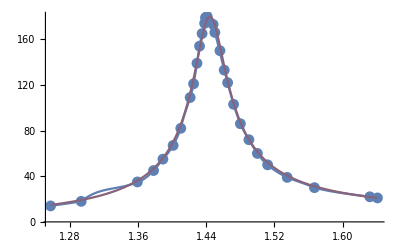

```mathematica
Show[%221,%229,%239]
```

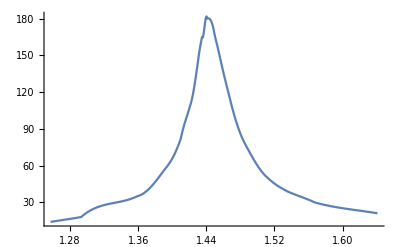

```mathematica
Plot[%228[x],{x,1.257,1.641}]
```

```mathematica
Plot[%226[x],{x,14.,180.}]
```

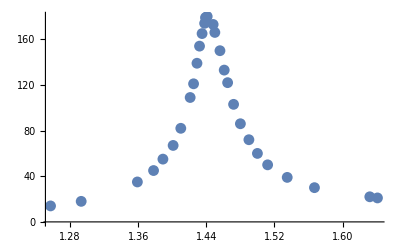

```mathematica
ListPlot[%]
```

```mathematica
list6={172,149,135,122,110,99,90,81,73,66,60,54,49,44,40,36}
```

{172,149,135,122,110,99,90,81,73,66,60,54,49,44,40,36}

```mathematica
list6=Log[#]&/@list6
```

{Log[172],Log[149],Log[135],Log[122],Log[110],Log[99],Log[90],Log[81],Log[73],Log[66],Log[60],Log[54],Log[49],Log[44],Log[40],Log[36]}

```mathematica
Length[list6]
```

16

17

```mathematica
(Sum[list6[[i]],{i,9,16}]-Sum[list6[[i]],{i,1,8}])/64//N
```

-0.102168

```mathematica
-0.08255927074403246
```

```mathematica
NSolve[%==-2 π/(√(1/x^2-1)),x]
```

{{x→-0.0162584},{x→0.0162584}}

```mathematica
ζ=0.021400882417732657
```

0.0214009

```mathematica
list7=1.444/{1.443,1.440,1.435,1.430,1.420,1.407,1.378,1.334,1.261,1.446,1.451,1.456,1.466,1.476,1.494,1.518,1.538,1.571,1.635};
list8={90.5,96.5,107.5,123,135.5,147.5,159,164,168,84.5,73,61,45.25,35,29.5,15.75,12.5,9,5.5};
```

```mathematica
Length/@{list7,list8}
```

{19,19}

```mathematica
ListInterpolation[list8,{list7}]
```

InterpolatingFunction[{{0.88318, 1.14512}}, <>]

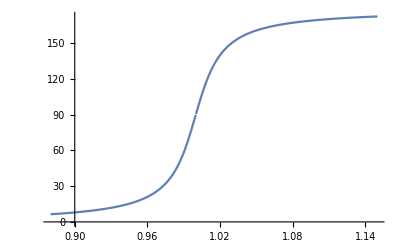

```mathematica
Plot[Piecewise[{{180/π*ArcTan[(2*0.01634)/((1/w)^2-1)],w<1},{180/π*ArcTan[(2*0.01634)/((1/w)^2-1)]+180,w>1}}],{w,0.88,1.15}]
```

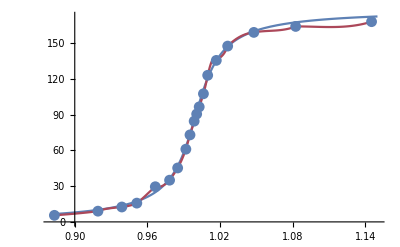

```mathematica
Show[%574,%573,ListPlot[{list7,list8}//Transpose]]
```

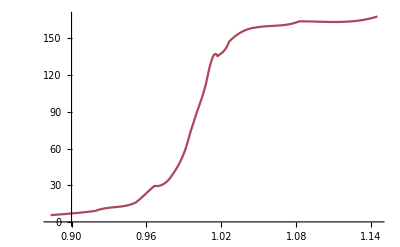

```mathematica
Plot[%571[x],{x,0.8831804281345564,1.1451229183187948},ColorFunction->"Rainbow"]
```

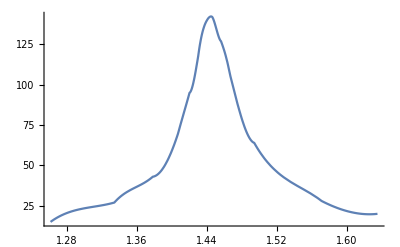

```mathematica
Plot[%274[x],{x,1.261,1.635}]
```

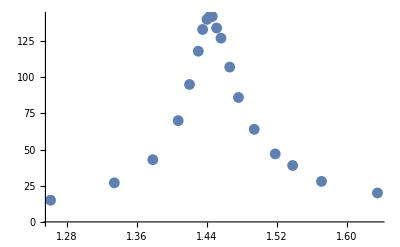

```mathematica
ListPlot[{list7,list8}//Transpose]
```

```mathematica
ζ
```

0.0214009

```mathematica
αm=109*2*ζ*√(1-ζ^2)
f[w_]:=αm/(√(4*ζ^2*(1.444/w)^2+(1-(1.444/w)^2)^2));
```

4.66432

```mathematica
list10=1.444/{1.444,1.440,1.435,1.428,1.415,1.421,1.411,1.393,1.366,1.326,1.278,1.255,1.453,1.457,1.467,1.483,1.5,1.526,1.558,1.599,1.634};
list11={89.5,98.25,101.5,112,133.5,127.5,137,149,157.5,162.5,165.5,166,73.5,66.5,53,37,27.5,19,13.75,10,7.5};
```

```mathematica
Length/@{list10,list11}
```

{21,21}

```mathematica
ListInterpolation[list11,{list10}]
```

InterpolatingFunction[{{0.883721, 1.1506}}, <>]

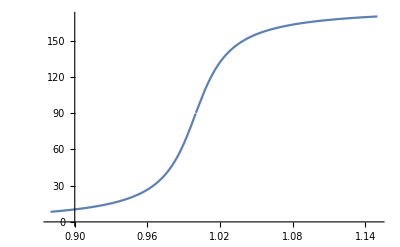

```mathematica
Plot[Piecewise[{{180/π*ArcTan[(2*0.0214)/((1/w)^2-1)],w<1},{180/π*ArcTan[(2*0.0214)/((1/w)^2-1)]+180,w>1}}],{w,0.88,1.15}]
```

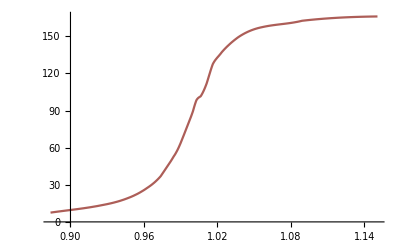

```mathematica
Plot[%585[x],{x,0.8837209302325582,1.150597609561753},ColorFunction->"Rainbow"]
```

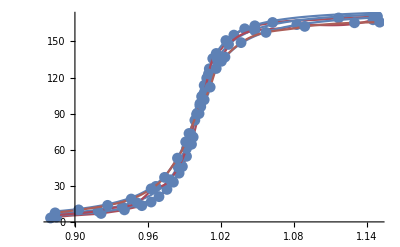

```mathematica
Show[%555,%575,%589]
```

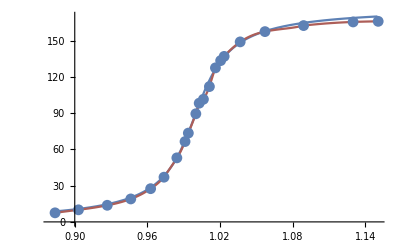

```mathematica
Show[%587,%588,ListPlot[{list10,list11}//Transpose]]
```

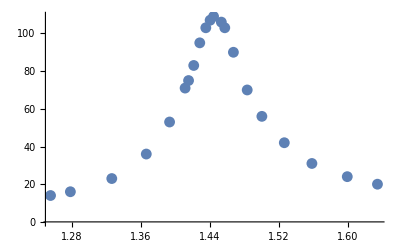

```mathematica
ListPlot[{list10,list11}//Transpose]
```

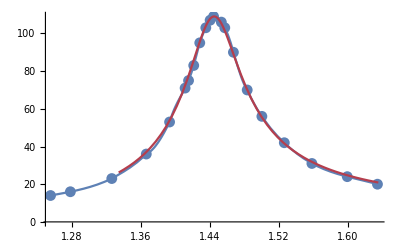

```mathematica
Show[%315,%314,%305,PlotLegends->"Damping2"]
```

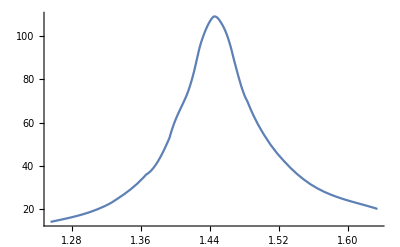

```mathematica
Plot[%313[x],{x,1.255,1.634}]
```

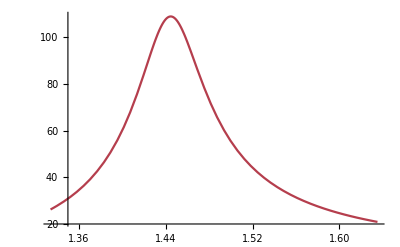

```mathematica
Plot[f[x],{x,1.255,1.},PlotRange->All,ColorFunction->"Rainbow"]
```

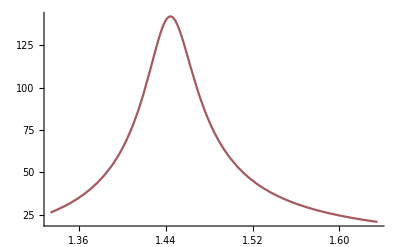

```mathematica
Plot[f[x],{x,1.334,1.635},PlotRange->All,ColorFunction->"Rainbow"]
```

```mathematica
(*for 3th*)
```

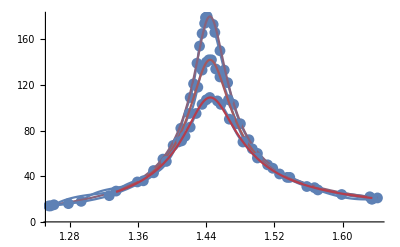

```mathematica
Show[%240,%288,%316]
```

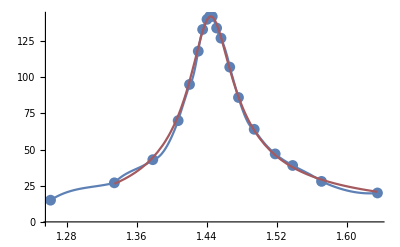

```mathematica
Show[%276,%275,%287]
```

```mathematica
list9={153,134,117,103,90,79,69,60,52,46,40,35}
```

{153,134,117,103,90,79,69,60,52,46,40,35}

```mathematica
list9=Log[#]&/@list9
```

{Log[153],Log[134],Log[117],Log[103],Log[90],Log[79],Log[69],Log[60],Log[52],Log[46],Log[40],Log[35]}

```mathematica
Length[list9]
```

12

```mathematica
(Sum[list9[[i]],{i,7,12}]-Sum[list9[[i]],{i,1,6}])/36//N
```

-0.134497